```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Matthew\Documents\Presentations\2017Aug25

## 2D Lattice Scattering Rates

```mathematica
Subscript[λ, rb]=780.241209686 10^-9;
Subscript[λ, li]=670.992 10^-9;
(*Subscript[λ, rb]=795 10^-9;*)
Subscript[λ, laser]=758 10^-9;
Subscript[λ, laser] = 1064 10^-9;
γ=2 π 6.065 10^6;
γ=2 π 5.746 10^6
γ = 2π 5.8724 10^6
hbar=1.0545 10^-34;
c=299792458;
e0=8.85 10^-12
w0=c/(2 π Subscript[λ, li])
Subscript[f, laser]=c/Subscript[λ, laser];
Subscript[f, li]=c/Subscript[λ, li];
δ= 2 π(Subscript[f, laser]-Subscript[f, li])

(*δ=2 π (60 10^9)*)
Is=(2 π^2 hbar γ c)/(3 Subscript[λ, rb]^3);
ec=1.6 10^-19;
μ=3.584 10^-29 ec/hbar;
```

3.61032×10^7

3.68974×10^7

8.85×10^-12

7.11088×10^13

-1.03691×10^15

```mathematica
Subscript[G, sc][I_]:=γ/2(I/Is)/(1+I/Is+4(δ/γ)^2)
Subscript[ψ, wv][x_,n_,m_]:=(((2 π)^2 √n)/π)^(1/4)Exp[(-(2π)^2)/2 √n x^2]HermiteH[m,x]
```

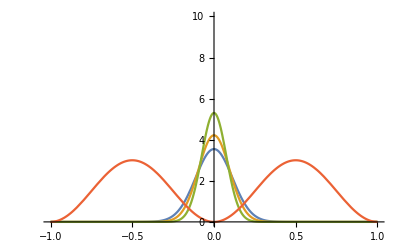

```mathematica
Plot[{(Subscript[ψ, wv][x,1,0])^2,(Subscript[ψ, wv][x,2,0])^2,(Subscript[ψ, wv][x,5,0])^2,3-3 Cos[x π]^2},{x,-1,1},
PlotRange-> {{-1,1},{0,10}}]
```

```mathematica
ItoEr[I_]:=√I μ / (1.24 10^3)
ErtoI[n_]:=hbar 1.24 10^3 n/μ^2
```

```mathematica
GSCBLUED2[n_]:=NIntegrate[n (1-Cos[x π]^2)  (2 π  1.24 10^3)Subscript[γ, rb]/Subscript[δ, rb](Subscript[ψ, wv][x,n,0])^2,{x,-1,1}]
GSCBLUED1[n_]:=NIntegrate[n (1-Cos[x π]^2)(2 π  1.24 10^3)Subscript[γ, rb]/(2 π 60 10^9)(Subscript[ψ, wv][x,n,0])^2,{x,-1,1}]
(*GSCRED[n_]:=NIntegrate[n (Cos[x π]^2) 1.24 10^3(680/532)^2 γ/δ(Subscript[ψ, wv][x,n,0])^2,{x,-1,1}]*)

GSCRED[n_]:=NIntegrate[n (Cos[x π]^2)( 2 π 25 10^3)Subscript[γ, li]/Subscript[δ, li](Subscript[ψ, wv][x,n,0])^2,{x,-1,1}]
GSCBLUEDLI[n_]:=NIntegrate[n (1-Cos[x π]^2)( 2 π  25 10^3)Subscript[γ, li]/Subscript[δ, li](Subscript[ψ, wv][x,n,0])^2,{x,-1,1}]
```

### Heating Calculations for Single Photon scattering events

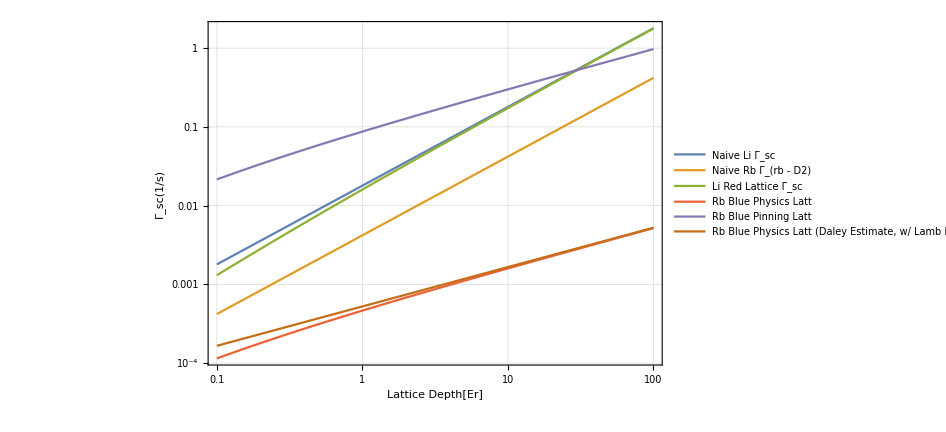

```mathematica
Subscript[λ, li]=670.992 10^-9;
Subscript[λ, laser] = 1064 10^-9;
Subscript[δ, li]= 2 π(Subscript[f, laser]-Subscript[f, li]);
Subscript[γ, li] = 2π 5.8724 10^6;

Subscript[λ, rb]=780.241209686 10^-9;
Subscript[λ, laser]=758 10^-9;
Subscript[γ, rb] = 2π  6.065 10^6;
Subscript[f, laser]=c/Subscript[λ, laser];
Subscript[f, rb]=c/Subscript[λ, rb];
Subscript[δ, rb]= 2 π(Subscript[f, laser]-Subscript[f, rb]);

(*I'm uncertain about the factor of 1/4 in the Daley paper... but It makes them agree at large depth*)
LogLogPlot[{Abs[Subscript[γ, li]/Subscript[δ, li] 2 π 24.9 10^3 x],
Abs[Subscript[γ, rb]/Subscript[δ, rb] 2 π 1.24 10^3 x],
Abs[GSCRED[x]],
Abs[GSCBLUED2[x]],
Abs[GSCBLUED1[x]],
Abs[Subscript[γ, rb]/Subscript[δ, rb] 2 π 1.24 10^3 x /4]( 4 x)^(-1/2)},
{x,0.1,100},
GridLines-> Automatic,
PlotStyle-> {Thick},
ImageSize-> 700,
Frame-> True,
FrameLabel-> {"Lattice Depth[Er]","Γ_sc(1/s)","Single Photon Scattering Rates for Li and Rb Exps"},
PlotLegends-> {"Naive Li Γ_sc","Naive Rb Γ_(rb - D2)","Li Red Lattice Γ_sc","Rb Blue Physics Latt","Rb Blue Pinning Latt","Rb Blue Physics Latt (Daley Estimate, w/ Lamb Dicke)"}]
```

```mathematica
GSCRED[10]/(2 π)
```

-0.00438283

## Axial Lattice Scattering? (Remember, it is mostly DC Light)

```mathematica
Subscript[λ, rb]=780.241209686 10^-9;
Subscript[λ, laser]=758 10^-9;
Subscript[γ, rb] = 2π  6.065 10^6;
Subscript[f, laser]=c/Subscript[λ, laser];
Subscript[f, rb]=c/Subscript[λ, rb];
Subscript[δ, rb]= 2 π(Subscript[f, laser]-Subscript[f, rb]);

Wo=100 10^-6;
zr[wo_]:=(π wo^2)/Subscript[λ, laser]
Wr[z_,wo_]:=wo √(1+(z/zr[wo]))
Ilatt[z_,r_,wo_,po_]:=(2 po)/(wo^2 π)(wo/Wr[z,wo])^2 Exp[(- 2 r^2)/Wr[z,wo]^2]
```

```mathematica
Subscript[Γ, scAxial][r_,z_,wo_,po_]:=(3 π c^2)/(2 hbar (2 π Subscript[f, rb])^3)(Subscript[f, laser]/Subscript[f, rb])^3(Subscript[γ, rb]/(-Subscript[δ, rb])+Subscript[γ, rb]/(2 (2 π Subscript[f, laser])+ Subscript[δ, rb]))Ilatt[z,r,wo,po]
```

```mathematica
Plot[Abs[(3 π c^2)/(2 hbar (2 π Subscript[f, rb]))(Subscript[γ, rb]/Subscript[δ, rb])(2 P)/((100 10^-6)^π)],{P,0,0.1}]
```

-Graphics-

```mathematica
Subscript[λ, rb]=780.241209686 10^-9;
Subscript[λ, laser]=758 10^-9;
Subscript[γ, rb] = 2π  6.065 10^6;
Subscript[f, laser]=c/Subscript[λ, laser];
Subscript[f, rb]=c/Subscript[λ, rb];
Subscript[δ, rb]= 2 π(Subscript[f, laser]-Subscript[f, rb]);
Abs[(3 π c^2)/(2 hbar (2 π Subscript[f, rb])^3)(Subscript[γ, rb]/Subscript[δ, rb])^2(2 0.1)/((100 10^-6)^2 π)]
```

0.525897

```mathematica
h
```

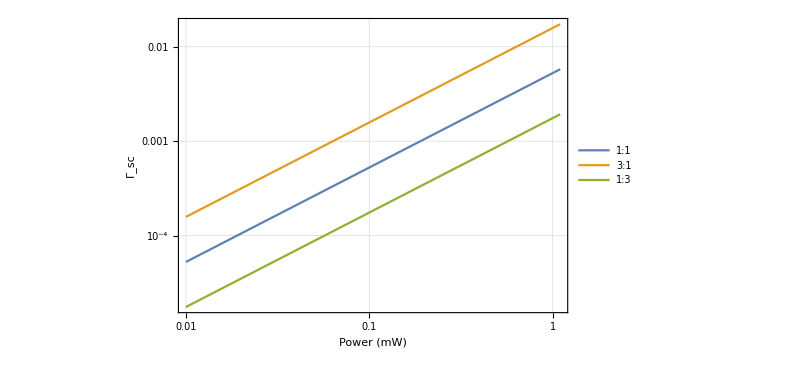

```mathematica
LogLogPlot[{Abs[(3 π c^2)/(2 hbar (2 π Subscript[f, rb])^3)(Subscript[γ, rb]/Subscript[δ, rb])^2(2 P/1000)/((100 10^-6)(100 10^-6)π)],
Abs[(3 π c^2)/(2 hbar (2 π Subscript[f, rb])^3)(Subscript[γ, rb]/Subscript[δ, rb])^2(2 P/1000)/((100 10^-6)(100 10^-6/3)π)],
Abs[(3 π c^2)/(2 hbar (2 π Subscript[f, rb])^3)(Subscript[γ, rb]/Subscript[δ, rb])^2(2 P/1000)/((100 10^-6)(3 100 10^-6)π)]}
,{P ,0.01,1.1},
GridLines-> Automatic,
Frame -> True,
PlotLegends-> {"1:1","3:1","1:3"},
ImageSize-> 600,
FrameLabel-> {"Power (mW)","Γ_sc","Single-Photon Axial Scattering Rate, 100um waist" }]
```

```mathematica
Rs[n1_,n2_,θ_]:=Abs[(n1 Cos[θ]-n2 √(1-(n1/n2 Sin[θ])^2))/(n1 Cos[θ]+n2 √(1-(n1/n2 Sin[θ])^2))]^2
Rp[n1_,n2_,θ_]:=Abs[(n1 √(1-(n1/n2 Sin[θ])^2)-n2 Cos[θ])/(n1 √(1-(n1/n2 Sin[θ])^2)+n2 Cos[θ])]^2
```

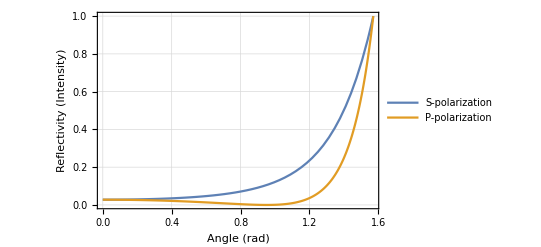

```mathematica
Plot[{Rs[1,1.4,x],Rp[1,1.4,x]},{x,0,π/2},
PlotRange-> {{0, π/2},{0,1}},
Frame-> True,
GridLines-> Automatic,
FrameLabel-> {"Angle (rad)","Reflectivity (Intensity)","Fresnel Coefficients"},
PlotLegends-> {"S-polarization","P-polarization"}]
```

```mathematica
√Rs[1,1.45,π/2((90-15)/90)]
Rp[1,1.45,π/2((90-15)/90)]
```

0.613774

0.109231

```mathematica
√Rs[1,1.45,π/2((90-2)/90)]
Rp[1,1.45,π/2((90-14.5)/90)]
```

0.935698

0.118593

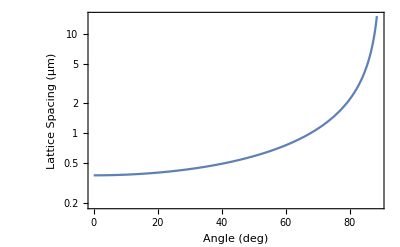

```mathematica
LogPlot[0.758/2/Cos[x  π /180],{x,0.01,90},
PlotRange-> {{0.01,89},{0.765/4,15}},
GridLines-> Automatic,
Frame-> True,
FrameLabel-> {"Angle (deg)","Lattice Spacing (μm)","Z-Confining Lattice"}]
```

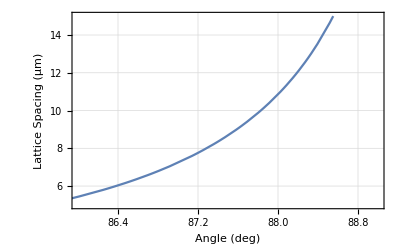

```mathematica
Plot[{0.758/2/Cos[x  π /180]},{x,0.01,90},
PlotRange-> {{86,89},{5,15}},
GridLines-> Automatic,
Frame-> True,
FrameLabel-> {"Angle (deg)","Lattice Spacing (μm)","Z-Confining Lattice (Big Lattice Region)"}]
```

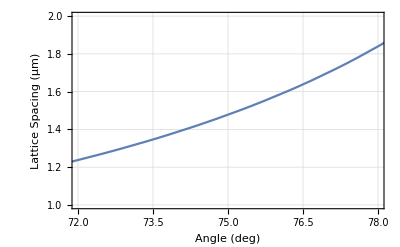

```mathematica
Plot[0.765/2/Cos[x  π /180],{x,0.01,90},
PlotRange-> {{72,78},{1,2}},
GridLines-> Automatic,
Frame-> True,
FrameLabel-> {"Angle (deg)","Lattice Spacing (μm)","Z-Confining Lattice (Axial LAttice Region)"}]
```

```mathematica
Alatt[th_]:=0.758/2/Cos[th π /180]
Manipulate[
Plot[{Abs[1/(√2)Exp[-I x 2 π/Alatt[thaxial]/2 - I π/2]+1/(√2)√Rs[1,1.45,π/2(thaxial/90)] Exp[I x 2 π/Alatt[thaxial]/2 +I π/2]]^2,
Abs[1/(√2)Exp[-I x 2 π/Alatt[thbig]/2 - I π/2]+1/(√2) √Rs[1,1.45,π/2(thbig/90)] Exp[I x 2 π/Alatt[thbig]/2+ I π/2]]^2},{x,0,11},
PlotRange-> {{0,11},{0,2}},
PlotLegends-> {"Axial Lattice","Big Lattice"},
ImageSize-> 600,
GridLines-> Automatic,
Frame-> True,
FrameLabel-> {"Spacing (μm)","Depth (Itensity), 1-normalized to incoming power","Axial Confining Lattices"}],
{{thaxial,75},0,90},
{{thbig,87.5},0,90}]
```

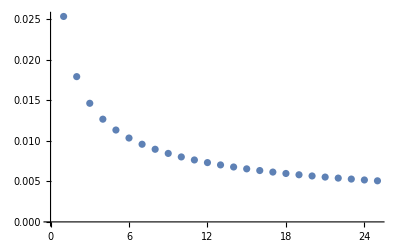

```mathematica
ur=Table[NIntegrate[Abs[Subscript[ψ, wv][x,n,0]]^2 Abs[Subscript[ψ, wv][x,n,1]]^2,{x,-4 π, 4 π}]/NIntegrate[Abs[Subscript[ψ, wv][x,n,0]]^2 Abs[Subscript[ψ, wv][x,n,0]]^2,{x,- 4 π,4 π}],{n,1,25}];
ListPlot[ur]
```

```mathematica
((1+√Rs[1,1.45,π/2((90-2)/90)])^2-(1-√Rs[1,1.45,π/2((90-2)/90)])^2)/2
```

1.8714

```mathematica
BigLattDC=(1+Rs[1,1.45,π/2((90-2.32)/90)]-2.*(√Rs[1,1.45,π/2((90-2.32)/90)]))200
AxialLattDC=(1+Rs[1,1.45,π/2((90-15)/90)]-2.*(√Rs[1,1.45,π/2((90-15)/90)]))200
```

1.10085

29.8341

```mathematica
GSCBLUEDPhys[n_]:=NIntegrate[n (1-Cos[x π]^2)( 2 π 1.24 10^3)Subscript[γ, rb]/Subscript[δ, rb](Subscript[ψ, wv][x,n,0])^2,{x,-1,1}]
GSCBLUEDPin[n_]:=NIntegrate[n (1-Cos[x π]^2) (2 π 1.24 10^3)Subscript[γ, rb]/(2 π 60 10^9)(Subscript[ψ, wv][x,n,0])^2,{x,-1,1}]
GSCBLUEDBigPhys[n_]:=NIntegrate[n (1-Cos[x π]^2) (2 π  1.24 10^3)(0.68/9.2)^2 Subscript[γ, rb]/Subscript[δ, rb](Subscript[ψ, wv][x,n,0])^2,{x,-1,1}]
GSCBLUEDAxPhys[n_]:=NIntegrate[n (1-Cos[x π]^2) (2 π  1.24 10^3)(0.68/1.5)^2 Subscript[γ, rb]/Subscript[δ, rb](Subscript[ψ, wv][x,n,0])^2,{x,-1,1}]
```

```mathematica
BigLatticeSPRate=Abs[(3 π c^2)/(2 hbar (2 π Subscript[f, rb])^3)(Subscript[γ, rb]/Subscript[δ, rb])^2(2 BigLattDC/1000)/((150 10^-6)(150 10^-6/2.6)π)]
AxialLatticeSPRate=Abs[(3 π c^2)/(2 hbar (2 π Subscript[f, rb])^3)(Subscript[γ, rb]/Subscript[δ, rb])^2(2 AxialLattDC/1000)/((150 10^-6)(150 10^-6)π)]
PhysLat2D1Rate=GSCBLUEDPhys[60]
PhysLat2D2Rate=GSCBLUEDPhys[8]
PhysBigLatRate=GSCBLUEDBigPhys[9404]
PhysAxLatRate = GSCBLUEDAxPhys[250]

Rin2D1=0.0002;
Rin2D1=0;
Rin2D2=0.001;
Rin2D2=0;
```

0.00668987

0.0697318

0.00399344

0.00141826

0.000277204

0.00168903

```mathematica
Subscript[Γ, TotalBig]=BigLatticeSPRate+PhysLat2D1Rate+PhysLat2D2Rate+PhysBigLatRate
```

0.0123788

```mathematica
Subscript[Γ, TotalAxial]=AxialLatticeSPRate+PhysLat2D1Rate+PhysLat2D2Rate+PhysAxLatRate
```

0.0768325

```mathematica
N[1/0.0768]
```

13.0208

```mathematica
N[1/15]
```

0.0666667

```mathematica
Pones[n_,t_,g_]:=(n Exp[-n g t]+(1-Exp[- n g t])(n-2))/n
Phole[n_,t_,g_]:=(1-Exp[- n g t])/n
Pdoublon[n_,t_,g_]:=(1-Exp[- n g t])/n
```

```mathematica
SVN[n_,t_,g_]:=-Pones[n,t,g]Log[Pones[n,t,g]]-Phole[n,t,g]Log[Phole[n,t,g]]-Pdoublon[n,t,g]Log[Pdoublon[n,t,g]]
```

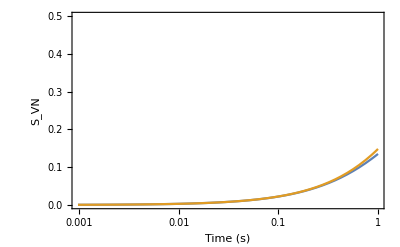

```mathematica
LogLinearPlot[{SVN[24,t,0.015],{SVN[8,t,0.015]}},{t,0,1},
GridLines-> Automatic,
PlotRange-> {{0,1}{0,0.5}},
Frame-> True,
FrameLabel-> {"Time (s)","S_VN","Entropy Growth from Scattering? γ=0.015 Hz + offset?"}]
```

```mathematica
(0.06/0.00578)/200
```

0.0519031

```mathematica
Solve[1+r^2-2r==0.05,r]
```

{{r→0.776393},{r→1.22361}}

```mathematica
Solve[Rs[1,1.4,t]==0.6027,t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→-1.5708+0.872618 ⅈ},{t→-1.44612},{t→1.44612},{t→1.5708-0.872618 ⅈ}}

```mathematica
(0.776393)^2
```

0.602786

```mathematica
90*1.44612/(π/2)
```

82.8566

3.05186

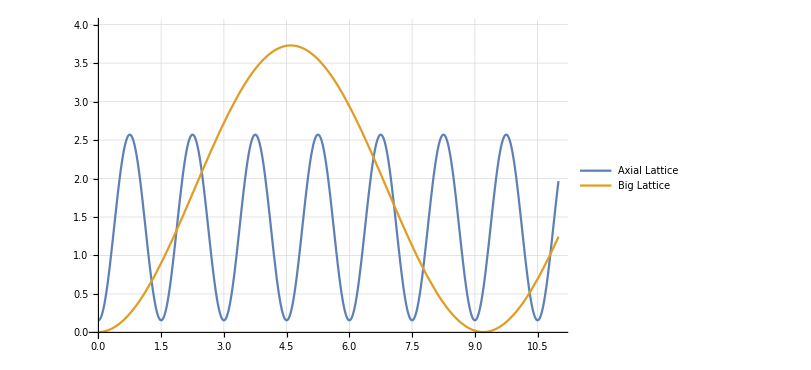

```mathematica
(0.765)/2/Sin[7.2 /90 * π/2]
Plot[{Abs[Exp[-I x 2 π/1.5/2 - I π/2]+√Rs[1,1.4,π/2((90-14.5)/90)] Exp[I x 2 π/1.5/2 +I π/2]]^2,
Abs[Exp[-I x 2 π/9.2/2 - I π/2]+√Rs[1,1.4,π/2((90-2)/90)] Exp[I x 2 π/9.2/2+ I π/2]]^2},{x,0,11},
PlotRange-> {{0,11},{0,4}},
PlotLegends-> {"Axial Lattice","Big Lattice"},
ImageSize-> 600,
GridLines-> Automatic]
```

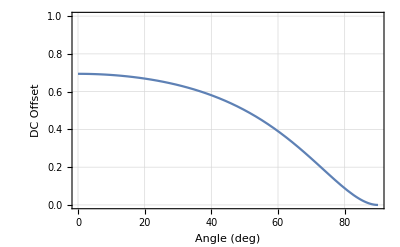

```mathematica
rfield[th_]:=√Rs[1,1.4,π/2(th/90)]
Plot[1+rfield[th]^2-2 rfield[th],{th,0,90},
PlotRange-> {{0,90},{0,1}},
GridLines-> Automatic,
Frame-> True,
FrameLabel-> {"Angle (deg)","DC Offset","DC Offset from Fresnel Coefficient Reflection"}]
```

```mathematica
1+0.04-2 √0.04
1+0.04+2 √0.04
```

0.64

1.44

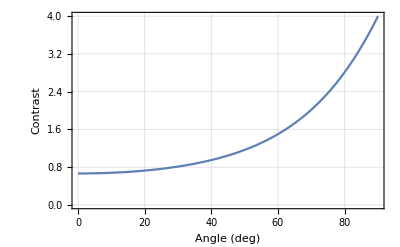

```mathematica
Plot[ 4 rfield[th],{th,0,90},
PlotRange-> {{0,90},{0,4}},
GridLines-> Automatic,
Frame-> True,
FrameLabel-> {"Angle (deg)","Contrast","Contrast from Fresnel Coefficient Reflection"}]
```

```mathematica
Rs[1,1.45,π/2((90-15)/90)]
```

0.376719